```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
α = 0.1;C0=0.4;T=60; θ1=30;θ2=1.5;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=300;
Ct[t_]=Which[Mod[t,T]<α T,1,Mod[t,T]<α T+(1-C0)/(θ1 /T)1,1-(Mod[t,T]-α T)θ1/ T, Mod[t,T]<T-(1-C0)/(θ2 /T),C0, True,C0+(Mod[t,T]-T+(1-C0)/(θ2/ T))θ2/ T];
Ctd[t_]=Which[Mod[t,T]<α T,0,Mod[t,T]<α T+(1-C0)/(θ1/ T),-θ1/ T, Mod[t,T]<T-(1-C0)/(θ2/ T),0, True,θ2/ T];
```

```mathematica
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;

{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.2(1-C0)/θ1];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},PlotRange->{-2.5,2},ColorFunction->Function[{t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False,PlotLegends->Placed[StringJoin["C0=",ToString[C0],", T= ",ToString[T],", α= ",ToString[α],", θ1= ",ToString[θ1],", θ2= ",ToString[θ2],"\n ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above]];
capacitance=Plot[{Ct[t]},{t,0,maxtime},PlotPoints->10000,MaxRecursion->3,PlotStyle->Orange];

g1=Show[voltage, capacitance]
Export["Fig5b.png",g1]
```

-Graphics-

Fig5b.png

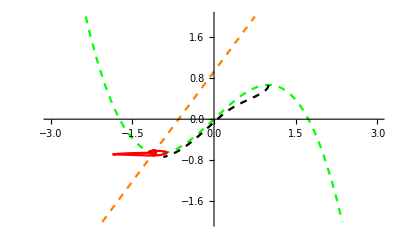

```mathematica
(*Phase plane*)
g1=ParametricPlot[{{V[t],W[t]}},{t,0,30},ColorFunction->Function[{x,y,t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False];
g2=Plot[{v-v^3/3,(v+β)/γ},{v,-3,3},PlotRange->{-2,2},PlotStyle->{{Green,Dashed},{Orange,Dashed}}];
g3=ListPlot[{{v0,w0}},PlotStyle->{Red}];
maxtimesep=26.5;
{Vsep,Wsep}=NDSolveValue[{-v'[t]== v[t]-v[t]^3/3-w[t],-w'[t]==ep(v[t]-γ w[t]+β),v[0]==1,w[0]==2/3},{v,w},{t,0,maxtimesep}];
separatrix=ParametricPlot[{Vsep[t],Wsep[t]},{t,0,maxtimesep},PlotStyle->{Black,Dashed}];
Show[g2,g1,g3,separatrix]
```